# Eratosthenes Sieve

I need an efficient sieve for a number of problems.

## Original Sieve

Written without optimisation:

```mathematica
eratosSieve1[max_Real]:=Block[
{
integers=Range[2,max],
primes={2,3},
multiples,
cnt=1
},
multiples=integers[[;;;;2]];
While[
Last@primes<max,
cnt++;
multiples=Union@Join[multiples,NestWhileList[#+Last@primes&,Last@primes,#<max&]];
primes=Append[primes,SelectFirst[Complement[integers,multiples],#>Last@primes&,Break[]]];
];
{cnt,primes}
]
```

```mathematica
eratosSieve1[100.]
```

{25,{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}}

## Basic Optimisations

### Sqrt and Odd Optimisation

As from wiki: “As a refinement, it is sufficient to mark the numbers in step 3 starting from p2, as all the smaller multiples of p will have already been marked at that point. This means that the algorithm is allowed to terminate in step 4 when p2 is greater than n”

```mathematica
eratosSieve[max_Real]:=Block[
{
integers=N@Range[2,max],
newPrimes=2.,
multiples,
primes
},
multiples=integers[[;;;;2]];
While[
newPrimes^2<max,
multiples=Union@Join[multiples,NestWhileList[#+2*newPrimes&,newPrimes^2,#<max&]];
newPrimes=SelectFirst[Complement[integers,multiples],#>newPrimes&,Break[]];
(*Print[multiples]*)
];
primes=Join[{2.},Complement[integers,multiples]];
{Length[primes],primes}
]
```

```mathematica
odds=eratosSieve[1909.];//AbsoluteTiming
```

{0.00901,Null}

## Eradicate multiples of 3 and 5

As mentioned within http://www.cs.hmc.edu/~oneill/papers/Sieve-JFP.pdf, removing multiples of 2,3,5,7 eliminates ~77% of our work for large n

```mathematica
remove3s=Select[Range[1000000],Mod[#,3]=!=0&];//AbsoluteTiming
```

{0.84403,Null}

```mathematica
remove2357=Select[Range[1000000],AllTrue[{2,3,5,7},Function[x,Mod[#,x]=!=0]]&];//AbsoluteTiming
```

{3.42208,Null}

Add this to the function for large n:

```mathematica
Remove[eratosSieveSqrtOddWheel]
```

```mathematica
eratosSieveSqrtOddWheel[max_Real]:=Block[
{
integers=N@Range[2,max],
newPrimes=11.,
multiples,
primes,
new
},
multiples=(*Union@Join[{2.,3.,5.,7.},(*Select[integers,AnyTrue[{2.,3.,5.,7.},Function[x,Mod[#,x]==0]]&]*)Flatten@Table[NestWhileList[#+i&,i,#<max&],{i,{2.,3.,5.,7.}}],integers[[7;;;;2]]]*)
Union@Sort@Flatten@Table[NestWhileList[#+i&,i,#<max&],{i,{2.,3.,5.,7.}}]
;
While[
newPrimes^2<max,
multiples=Union@Join[multiples,new=NestWhileList[#+2*newPrimes&,newPrimes^2,#<max&]];
newPrimes=SelectFirst[Complement[integers,multiples],#>newPrimes&,Break[]];
(*Print[<|"newmultis"->new,"newprime"->newPrimes,"mults"->multiples|>]*)
];
primes=Join[{2.,3.,5.,7.},Complement[integers,multiples]];
{Length[primes],primes}
]
```

```mathematica
GeneralUtilities`AccurateTiming[sieve1=eratosSieve[1102303.];]
```

16.88026

```mathematica
GeneralUtilities`AccurateTiming[sieve2=eratosSieveSqrtOddWheel[1102303.];]
```

17.66497

```mathematica
sieve1==sieve2
```

True

## nth Prime

The nth prime is approximated by n*Log[n], but this is necessarily less than the value of the nth prime. So here’s an approximation for the first 100,000 primes:

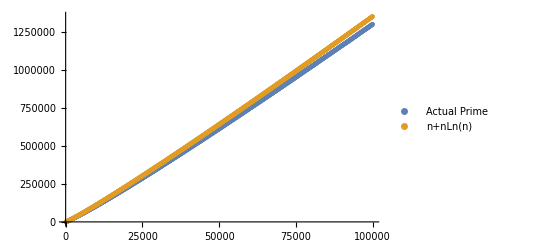

```mathematica
ListPlot[N@Transpose@Table[{{i,Prime[i]},{i,2*i+i*Log[i]}},{i,100,100000,100}],PlotLegends->{"Actual Prime","n+nLn(n)"}]
```

The nth prime function can effectively use this to generate integers:

```mathematica
nthPrimeByEratos[nth_]:=Block[
{
integers=N@Range[2,2*nth+nth*Log[nth]],
primes=2.,
multiples={},
cnt=0
},
While[
cnt<nth,
cnt++;
primes=SelectFirst[Complement[integers,multiples],#>primes&,Break[]];
multiples=Union@Join[multiples,NestWhileList[#+primes&,primes,#<2*nth+nth*Log[nth]&]];
];
{cnt,primes}
]
```

```mathematica
AbsoluteTiming[foo=nthPrimeByEratos[10001];]
```

{39.80294,Null}

```mathematica
foo
```

{10001,104743.}

```mathematica
Prime[10001]
```

104743

### New nth Prime

```mathematica
nthPrimeByEratos2[nth_]:=Block[
{
integers=N@Range[2,2*nth+nth*Log[nth]],
newprime=2.,
multiples={},
cnt=0
},
multiples=integers[[;;;;2]];
While[
cnt<nth-1,
cnt++;
newprime=SelectFirst[Complement[integers,multiples],#>newprime&,Break[]];
multiples=Union@Join[multiples,NestWhileList[#+newprime&,newprime,#<2*nth+nth*Log[nth]&]];
(*Print[<|"newprime"->newprime,"multiples"->multiples|>]*)
];
{cnt+1,newprime}
]
```

```mathematica
AbsoluteTiming[new=nthPrimeByEratos2[10001];]
```

{74.32884,Null}

```mathematica
new[[2]]
```

16433.

```mathematica
new[[1]]
```

5

```mathematica
Mod[2^60]
```

Mod::argtu: Mod called with 1 argument; 2 or 3 arguments are expected.

Mod[1152921504606846976]

```mathematica
AbsoluteTiming[old=nthPrimeByEratos[10001];]
```

{47.33134,Null}

```mathematica
Prime[105]
```

571